# Sound Waves

## One wave

```mathematica
Clear["Global`*"]
```

```mathematica
k=1000;
```

```mathematica
f1[t_]=ⅇ^(ⅈ k t);
```

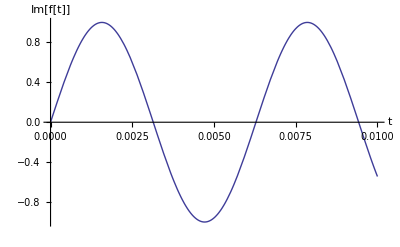

```mathematica
Plot[Im[f1[t]],{t,0,0.01},AxesLabel->{"t","Im[f[t]]"}]
```

```mathematica
Play[Im[f1[t]],{t,0,5}]
```

-Graphics-

## Superposition of two waves (beat)

```mathematica
k1=2000;
```

```mathematica
f1[t_]=ⅇ^(ⅈ k1 t);
```

```mathematica
k2=2002;
```

```mathematica
f2[t_]=ⅇ^(ⅈ k2 t);
```

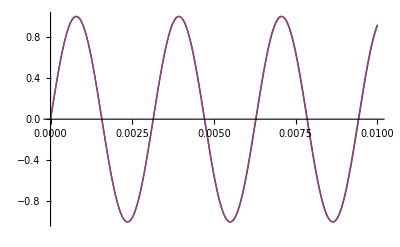

```mathematica
Plot[{Im[f1[t]],Im[f2[t]]},{t,0,0.01}]
```

```mathematica
f[t_]=f1[t]+f2[t]
```

ⅇ^(2000 ⅈ t)+ⅇ^(2002 ⅈ t)

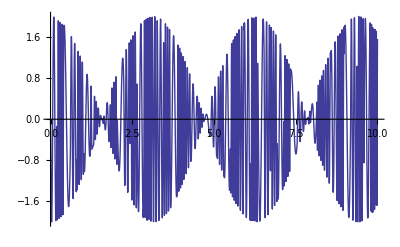

```mathematica
Plot[Im[f[t]],{t,0,10}]
```

```mathematica
Play[Im[f[t]],{t,0,10}]
```

-Graphics-

## Superposition of several waves (beat)

```mathematica
g[t_]=Sum[Sin[n t],{n,2000,2040,10}]
```

Sin[2000 t]+Sin[2010 t]+Sin[2020 t]+Sin[2030 t]+Sin[2040 t]

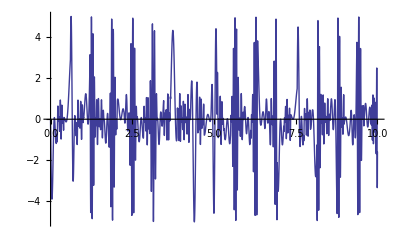

```mathematica
Plot[g[t],{t,0,10}]
```

```mathematica
Play[g[t],{t,0,10}]
```

-Graphics-

## Superposition of several discrete waves (periodic pulse)

The spectral density function

```mathematica
g[k_]:=1000/k
```

```mathematica
Table[g[k],{k,1000,10000,2000}]
```

{1,1/3,1/5,1/7,1/9}

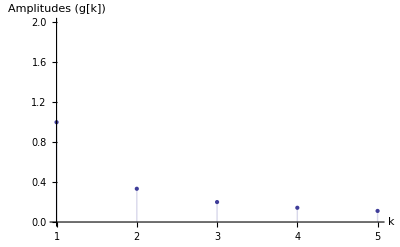

```mathematica
ListPlot[Table[g[k],{k,1000,10000,2000}],Filling->Axis,PlotRange->{0,2},AxesLabel->{"k","Amplitudes (g[k])"}]
```

periodic pulse

```mathematica
f[x_]=Sum[g[k] ⅇ^(ⅈ  k x),{k,1000,10000,2000}]
```

ⅇ^(1000 ⅈ x)+1/3 ⅇ^(3000 ⅈ x)+1/5 ⅇ^(5000 ⅈ x)+1/7 ⅇ^(7000 ⅈ x)+1/9 ⅇ^(9000 ⅈ x)

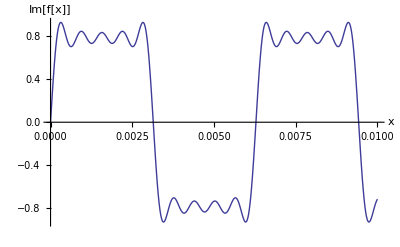

```mathematica
Plot[Im[f[x]],{x,0,0.01},AxesLabel->{"x","Im[f[x]]"}]
```

```mathematica
Play[Im[f[t]],{t,0,10}]
```

-Graphics-

## Continuous superposition of several waves (Non-periodic pulse or wave pack)

```mathematica
Clear["Global`*"]
```

The spectral distribution of the amplitude

Gaussian pulses

```mathematica
g[k_]=PDF[NormalDistribution[Subscript[k, 0],σ],k]/.{Subscript[k, 0]->0,σ->3}
```

(ⅇ^(-k^2/18))/(3 √(2 π))

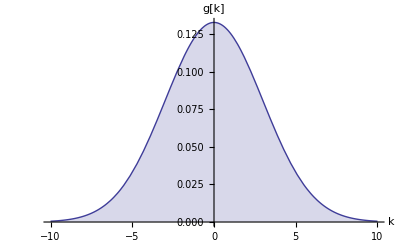

```mathematica
Plot[g[k],{k,-10,10},Filling->Axis,PlotRange->All,AxesLabel->{"k","g[k]"}]
```

Wave pack

```mathematica
f[x_]=∫_(-∞)^∞ g[k] ⅇ^(ⅈ k x)ⅆk
```

ⅇ^(-(9 x^2)/2)

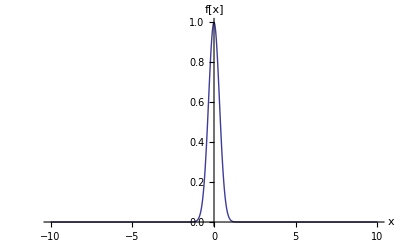

```mathematica
Plot[f[x],{x,-10,10},PlotRange->All,AxesLabel->{"x","f[x]"}]
```

```mathematica
Play[f[t],{t,0,10}]
```

-Graphics-